NDSolve::nderr: Error test failure at t == 26.6845; unable to continue.

{{d→InterpolatingFunction[{{0.,26.6845}},<>],x→InterpolatingFunction[{{0.,26.6845}},<>],m→InterpolatingFunction[{{0.,26.6845}},<>],r→InterpolatingFunction[{{0.,26.6845}},<>]}}

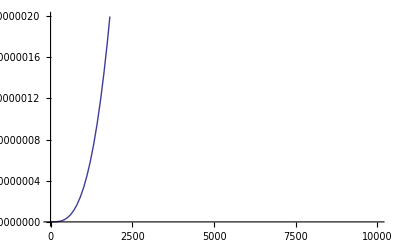

{-Graphics3D-,-Graphics3D-}

```mathematica
sol1=NDSolve[{d'[t]==.05*d[t]-.002*d[t]*x[t]- .01*d[t]*m[t]+d[t]*r[t],x'[t]== 100+.0001*x[t]-.002*d[t]*x[t]- .01*x[t]*m[t]+x[t]*r[t],m'[t]==.05*m[t]-.0005*d[t]*m[t]- .001*x[t]*m[t]+Sqrt[m[t]*r[t]], r'[t]== r[t](1-r[t]), d[0]==5,x[0]==5,m[0]==1,r[0]==1},{d,x,m,r},{t,0,10000}]

Plot[Evaluate[{r[t]}/.sol1],{t,0,10000}]

eqns = {
x'[t]==x[t](2+μ-10(x[t]^2+y[t]^2)) + z[t]^2 + y[t]^2 +2 y[t],
y'[t]==-z[t]^3-(1+y[t])(z[t]^2+y[t]^2+2 y[t])-4 x[t]+μ y[t],
z'[t]==(1+y[t]) z[t]^2 +x[t]^2-ϵ};

Table[Block[{ϵ=0.0357,T=1000},
sol = First[NDSolve[{eqns, x[0]==y[0]==z[0]==1},{x,y,z},{t,0,T}, MaxSteps->∞]];
ParametricPlot3D[Evaluate[{x[t],y[t],z[t]} /. sol],{t,T/4,T}, BoxRatios->1,PlotPoints->1000,PlotRange->All]],{μ,.455,.456,.001}]
```